```mathematica
eq = x - ((1-α)(γ-1+ δ))/(1/β - (1-δ))//FullSimplify
```

x+((-1+α) β (-1+γ+δ))/(1+β (-1+δ))

```mathematica
δsub = Solve[eq==0, δ]⟦1⟧//FullSimplify
```

{δ→(x (-1+β)+β (-1+α+γ-α γ))/((-1+x+α) β)}

```mathematica
δparam = δ/.δsub/.β-> 0.99/.α-> 2/3/.γ-> 1.03^(1/4)
```

(1.0101 (0.00244763-0.01 x))/(-1/3+x)

```mathematica
(1.0101010101010102 (0.00990000000000001-0.010000000000000009 x))/(-1/3+x)
```

(1.0101 (0.0099-0.01 x))/(-1/3+x)

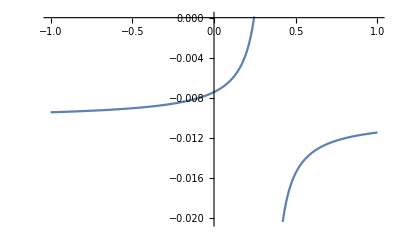

```mathematica
Plot[δparam, {x, -1, 1}]
```

```mathematica
δparam/.x-> 0.14
```

-0.0444096

```mathematica
δ/.δsub//TeXForm
```

\frac{\beta  (\alpha  (-\gamma )+\alpha +\gamma
   -1)+(\beta -1) x}{\beta  (\alpha +x-1)}